```mathematica
This file predicts the initial concetration of [MP] and [RQ] that is used to characterize the reporter reaction: MP+RQ<->MPR+Q
```

*****************************************

Case: B1P27-5.xlsx

{44.8627,44.8627,44.8627,44.8627,44.8627}

Concentration from Alexa signal

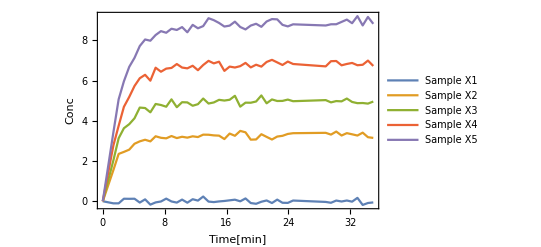

concBP (predicted from Cy3):{-0.0104451,2.61662,4.07585,5.75226,7.50307}

RQ_initial:44.8627

```mathematica
tend=250;(*final time of interest*)
samp=Table[i,{i,1,5,1}];(*sample of interest*)
injinfo=0;(*If injinfo =0, use conc before injection and time as avg of before and after, else use conc after injection and time as after injection*)
forward=1;(*1 if reaction forward going BP+RQ->BPR+Q, 0 otherwise*)
skip=0;(*skip timesteps after injection or not*)
FRQ=691.03;(*Fl Alexa density of RQ*)
FBPR=8261.9;(*Fl Alexa density of BPR*)
FBP=8993;(*Fl Cy3 of BP*)
printall=0;(*1 to print all intermedairy figuers, 0 for just concentration vs time figures*)

w1=1;(*Changes weight on point before injection*)
w2=0;(*changes weight on point after injection*)
(*All list of files used for data analysis of reporter characterization*)
files={"B1P27-5.xlsx","B1P28-5.xlsx","B1P29-5.xlsx","B1aP27-5.xlsx","B1aP28-5.xlsx","B1aP29-5.xlsx","B1bP27-5.xlsx","B1bP28-5.xlsx","B1bP29-5.xlsx"};

For[n=1,n<=1,n++,
(*Notes: files[[2]] has a jump. In normalized time units, the jump occurs at t=17 units, do not take data after that*)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["2. Reporters\\"];
(*SetDirectory["2. Reporters"];*)
data=Import[files[[n]],{"Sheets","Table All Cycles"}];
Print["*****************************************"];
Print["Case: ", files[[n]]];
(*Extract relevant data*)
For[i=1,i<=Length[data],i++,If[data[[i]][[1]]=="Content",Break[]]];
data=data[[i;;,2;;]];
(* 
data is as follows;
Time[min] Sample X1 Sample X2 Sample X3 Sample X4 Sample X5 Sample X6...;
0 8983 9948 9248 9686 9373 9062
0.53 8696 9316 10039 9228 9138 9028
0.92 8647 9180 9539 9510 9125 9608
1.3 8820 9767 9968 9609 9353 9411
....
...
*)

(*Stores the legends in this variable*)
samplename=data[[1]][[2;;]];
legend={};(*will remove samples of insignificance from samplename array and be used as the legend list*)
For[i=1,i<=Length[samplename],i++,
If[samplename[[i]]=="Control C1"||samplename[[i]]=="Control C2"||samplename[[i]]=="Control C3"||samplename[[i]]=="Positive control P"||samplename[[i]]=="Negative control N",,
AppendTo[legend,samplename[[i]]];
]];

inj=0(*Row number of Cy3 injection*);
save=0;(*Index number of last datapoint of Alexa signal*);

(*Extract column number of Poitive and Negative control (and extra conrols if exist). Also extract column number of Sample X1 and row number of Cy3 Injection*);
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C3"||data[[1]][[i]]=="Negative control N",Break[]]];iC3=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C2",Break[]]];iC2=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C1"||data[[1]][[i]]=="Positive control P",Break[]]];iC1=i;

For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Sample X1",Break[]]];iS0=i;
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="Inj.",c++;If[c==2,Break[]]]];inj0=i;(*first injection row number*)
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="Inj.",c++;If[c==3,Break[]]]];inj=i;(*second injection row number*)
If[printall==1,Print["Row number of Cy3 injection:", inj]];

(*Functions defined for further data processing*)
(*The "cut" function only takes data upto a certain time point*)
f[x_]:=0;
cut[x_,t_]:=(For[i=1,i<=Length[x[[1]]],i++,If[x[[1]][[i]][[1]]>t,Break[]];];ret={};
For[j=1,j<=Length[x],j++,AppendTo[ret,x[[j]][[1;;Min[i,Length[x[[j]]]]]]]];Return[ret];);

dnew=Array[f,Length[data[[1]]]-1];(*Stores all sample info*)
dnewfl=Array[f,Length[data[[1]]]-3];(*Stores all sample info minus controls*)
dnewfltem=dnewfl;

(***************************************************************************************)
(*Create a concentration array where each element stores a table of {time,fluoroscence} after injection for the different samples including +ve and -ve controls*)
For[i=2,i<=Length[data[[1]]],i++,dnew[[i-1]]=data[[2;;,{1,i}]];];

(*Find the second Inj. point and save the row number where the time before 2nd Inj. is 0. *)
c=1;For[i=1,i<=Length[dnew[[1]]],
i++,If[c==3,Break[]];
If[dnew[[1]][[i]][[2]]=="Inj.",c++];
If[c==3,For[j=i-1,j>=1,j--,If[dnew[[1]][[j]][[1]]==0.,save=j;Break[];]]]
];
For[i=1,i<=Length[dnew],i++,dnew[[i]]=dnew[[i]][[save;;]]];
inj=inj-save+1;
If[printall==1,Print["Number of datapoints in the 625/30 (Cy3) signal: ",inj]];
If[printall==1,Print["Index of the final datapoint of Alexa signal: ",save]];
If[printall==1,Print[inj,", ", save]];

(*dnew is Alexa, dnewtem is Cy3 signal*)

(*Extract Alexa signal and define time, conc at the injection point*)
For[i=2,i<=Length[data[[1]]],i++,
dnew[[i-1]]=data[[2;;save,{1,i}]](*Stores all datapoint of Alexa signal*);
If[dnew[[i-1]][[inj-1]][[2]]=="Inj.",If[injinfo==0,dnew[[i-1]][[inj-1]][[2]]=w1*dnew[[i-1]][[inj-2]][[2]]+w2*dnew[[i-1]][[inj]][[2]]],dnew[[i-1]][[inj-1]][[2]]=dnew[[i-1]][[inj]][[2]]];
If[dnew[[i-1]][[inj-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnew[[i-1]][[inj-1]][[1]]=w1*dnew[[i-1]][[inj-2]][[1]]+w2*dnew[[i-1]][[inj]][[1]],dnew[[i-1]][[inj-1]][[1]]=dnew[[i-1]][[inj]][[1]]];
]];





(*Extract Cy3 signal and define time, conc at the injection point*)
dnewtem=dnew;
For[i=2,i<=Length[data[[1]]],i++,
dnewtem[[i-1]]=data[[save+1;;,{1,i}]](*Stores all datapoint of Cy3 signal*);
If[dnewtem[[i-1]][[inj0-1]][[2]]=="Inj.",If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0-2]][[2]]],dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0]][[2]]];
If[dnewtem[[i-1]][[inj0-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0-2]][[1]],dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0]][[1]]];
]];



(*(*For[i=2,i<=Length[data[[1]]],i++,dnew[[i-1]]=data[[2;;save,{1,i}]](*Stores all datapoint of Cy3 signal*)];*)
For[i=2,i<=Length[data[[1]]],i++,dnewtem[[i-1]]=data[[save+1;;,{1,i}]](*Stores all datapoint of Cy3 signal*)];
*)

If[printall==1,Print["Alexa Signal:"]];
s1=ListPlot[dnew,Joined->True,PlotLegends->samplename];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];


(*Collect fluoroscence data from Cy3 to estimate initial BP*)
s1=ListPlot[dnewtem,Joined->True,PlotLegends->samplename];
If[printall==1,Print["Cy3 Signal:"]];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];


(*Update the Cy3 signal by subtracting negative control and updating time. 
Note inj-1 is impt bec "inj" was calculated on whole data, then the first name row was removed and inj. line was removed too*)
c=1;
 For[i=1,i<=Length[dnew],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1||i==iS0-1,,
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-If[injinfo==0,dnew[[i]][[inj-1]][[1]],dnew[[i]][[inj]][[1]]],dnew[[i]][[j]][[2]]-dnew[[iC3-1]][[j]][[2]](*-dnew[[iS0-1]][[j]][[2]]*)},{j,If[injinfo==0,inj-1,inj],Length[dnew[[i]]],1}];];
If[i==iS0-1,
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-If[injinfo==0,dnew[[i]][[inj-1]][[1]],dnew[[i]][[inj]][[1]]],dnew[[i]][[j]][[2]]-dnew[[iC3-1]][[j]][[2]]},{j,If[injinfo==0,inj-1,inj],Length[dnew[[i]]],1}];]];

c=1;
 For[i=1,i<=Length[dnewtem],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1||i==iS0-1,,
dnewfltem[[c++]]=Table[{dnewtem[[i]][[j]][[1]]-If[injinfo==0,dnewtem[[i]][[inj-1]][[1]],dnewtem[[i]][[inj]][[1]]],dnewtem[[i]][[j]][[2]]-dnewtem[[iC3-1]][[j]][[2]](*-dnew[[iS0-1]][[j]][[2]]*)},{j,If[injinfo==0,inj0-1,inj0],Length[dnewtem[[i]]],1}]];;
If[i==iS0-1,
dnewfltem[[c++]]=Table[{dnewtem[[i]][[j]][[1]]-If[injinfo==0,dnewtem[[i]][[inj-1]][[1]],dnewtem[[i]][[inj]][[1]]],dnewtem[[i]][[j]][[2]]-dnewtem[[iC3-1]][[j]][[2]]},{j,If[injinfo==0,inj0-1,inj0],Length[dnewtem[[i]]],1}];]
];

(*
(*subtract control C3 frm BP data*)
c=1; For[i=1,i<=Length[dnewtem],i++,If[i==iC2-1||i==iC1-1||i==iC3-1,Continue[],dnewfltem[[c++]]=Table[dnewtem[[i]][[j]][[2]]-dnewtem[[iC3-1]][[j]][[2]],{j,1,Length[dnewtem[[i]]],1}];]];*)
(*dnewfl=cut[dnewfl,tend];
dnewfltem=cut[dnewfltem,tend];*)

For[i=1,i<=5,i++,
For[j=1,j<=Length[dnewfl[[i]]],j++,
dnewfl[[i]][[j]][[2]]=0.5*(dnewfl[[i+5]][[j]][[2]]+dnewfl[[i]][[j]][[2]])*1.00]];

For[i=1,i<=5,i++,
For[j=1,j<=Length[dnewfltem[[i]]],j++,
dnewfltem[[i]][[j]][[2]]=0.5*(dnewfltem[[i+5]][[j]][[2]]+dnewfltem[[i]][[j]][[2]])]];

dnewfltem=dnewfltem[[samp]];
dnewfl=dnewfl[[samp]];

For[i=1,i<=Length[dnewfl],i++,
dnewfl[[i]][[1]][[2]]=dnewfl[[1]][[2]][[2]]];

For[i=1,i<=Length[dnewfltem],i++,
dnewfltem[[i]][[1]][[2]]=dnewfltem[[i]][[2]][[2]]];

If[printall==1,Print["Alexa Signal (normalized):"]];
s1=ListPlot[dnewfl,Joined->True,PlotLegends->legend];

If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];
If[printall==1,Print["Cy3 Signal (normalized):"]];
s1=ListPlot[dnewfltem,Joined->True,PlotLegends->legend];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];


(*Export Normalized Alexa and Cy3 signal*)
str=StringJoin[Characters[files[[n]]][[1;;-6]]];
data={dnewfl[[1]][[1;;,1]]};
data2={dnewfltem[[1]][[1;;,1]]};
For[i=1,i<=Length[dnewfl],i++,
AppendTo[data,dnewfl[[i]][[1;;,2]]];
AppendTo[data2,dnewfltem[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}];

plotdata=dnewfl;
ListPlot[plotdata,Joined->True,PlotLegends->legend[[samp]],BaseStyle->FontSize[8],PlotRange->All,Frame->True,FrameLabel->{"Time[min]","Fluoroscence"},FrameStyle->Thick];

(*Convert fluoroscence to concentrations*);
concRQ={};(*Will store list of initial [RQ] concentrations*)
crq=Mean[dnewfl[[1]][[2;;,2]]]/FRQ;

For[i=1,i<=Length[dnewfl],i++,
(*crq=dnewfl[[i]][[1]][[2]]/FRQ;
cbpr=dnewfl[[i]][[1]][[2]]/FBPR;
crq=Mean[dnewfl[[1;;,1]][[2;;,2]]]/FRQ;*)
For[j=1,j<=Length[dnewfl[[i]]],j++,
dnewfl[[i]][[j]][[2]]=(dnewfl[[i]][[j]][[2]]-crq*FRQ)/(FBPR-FRQ);];
AppendTo[concRQ,crq]];

Print[concRQ];

Print["Concentration from Alexa signal"];
For[j=1,j<=Length[dnewfl],j++,
dnewfl[[j]][[1]][[2]]=Mean[dnewfl[[1]][[2;;,2]]]];
g1=ListPlot[dnewfl[[1;;5]],Joined->True,PlotLegends->legend[[samp]],BaseStyle->FontSize[8],PlotRange->All,Frame->True,FrameLabel->{"Time[min]","Conc"},FrameStyle->Thick];
Print[g1];

(*Export files*)
ext={".","w","l"};
main=Characters[files[[n]]][[1;;-6]];
ext2={"R","Q","i"};
ext3={"B","P","i"};

ss1=StringJoin[Flatten[Append[main,ext]]];
ss2=StringJoin[Flatten[Append[Append[main,ext2],ext]]];
ss3=StringJoin[Flatten[Append[Append[main,ext3],ext]]];

dtemp=dnewfltem;
For[i=1,i<=Length[dtemp],i++,
For[j=1,j<=Length[dtemp[[i]]],j++,
dtemp[[i]][[j]][[2]]=dtemp[[i]][[j]][[2]]/FBP]];

If[printall==1,Print["Concentration from Cy3 Signal:"]];
s1=ListPlot[dtemp,Joined->True,PlotLegends->legend];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];

data={dtemp[[1]][[1;;,1]]};
For[i=1,i<=5,i++,
str=ss1;
AppendTo[data,dtemp[[i]][[1;;,2]]]];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];



(*Get BP initial from Cy3 signal*);
concV={};
For[i=1,i<=Length[dnewfltem],i++,
dnewfltem[[i]]=dnewfltem[[i]][[10;;]];
AppendTo[concV,Mean[dnewfltem[[i]]]/FBP];];


Print["concBP (predicted from Cy3):",concBP=concV[[1;;,2]]];
Print["RQ_initial:",crq];

(*Uncomment this*)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["2. Reporters\\Data"];
Export[ss1,dnewfl[[1;;5]]];(*Export experimental data of converted fluoroscence signal*)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["2. Reporters\\Conc"];
Export[ss2,crq];(*Export initial RQ obtained*)
Export[ss3,concBP](*Export the [BP] predicted from Cy3 signal*)
]
```

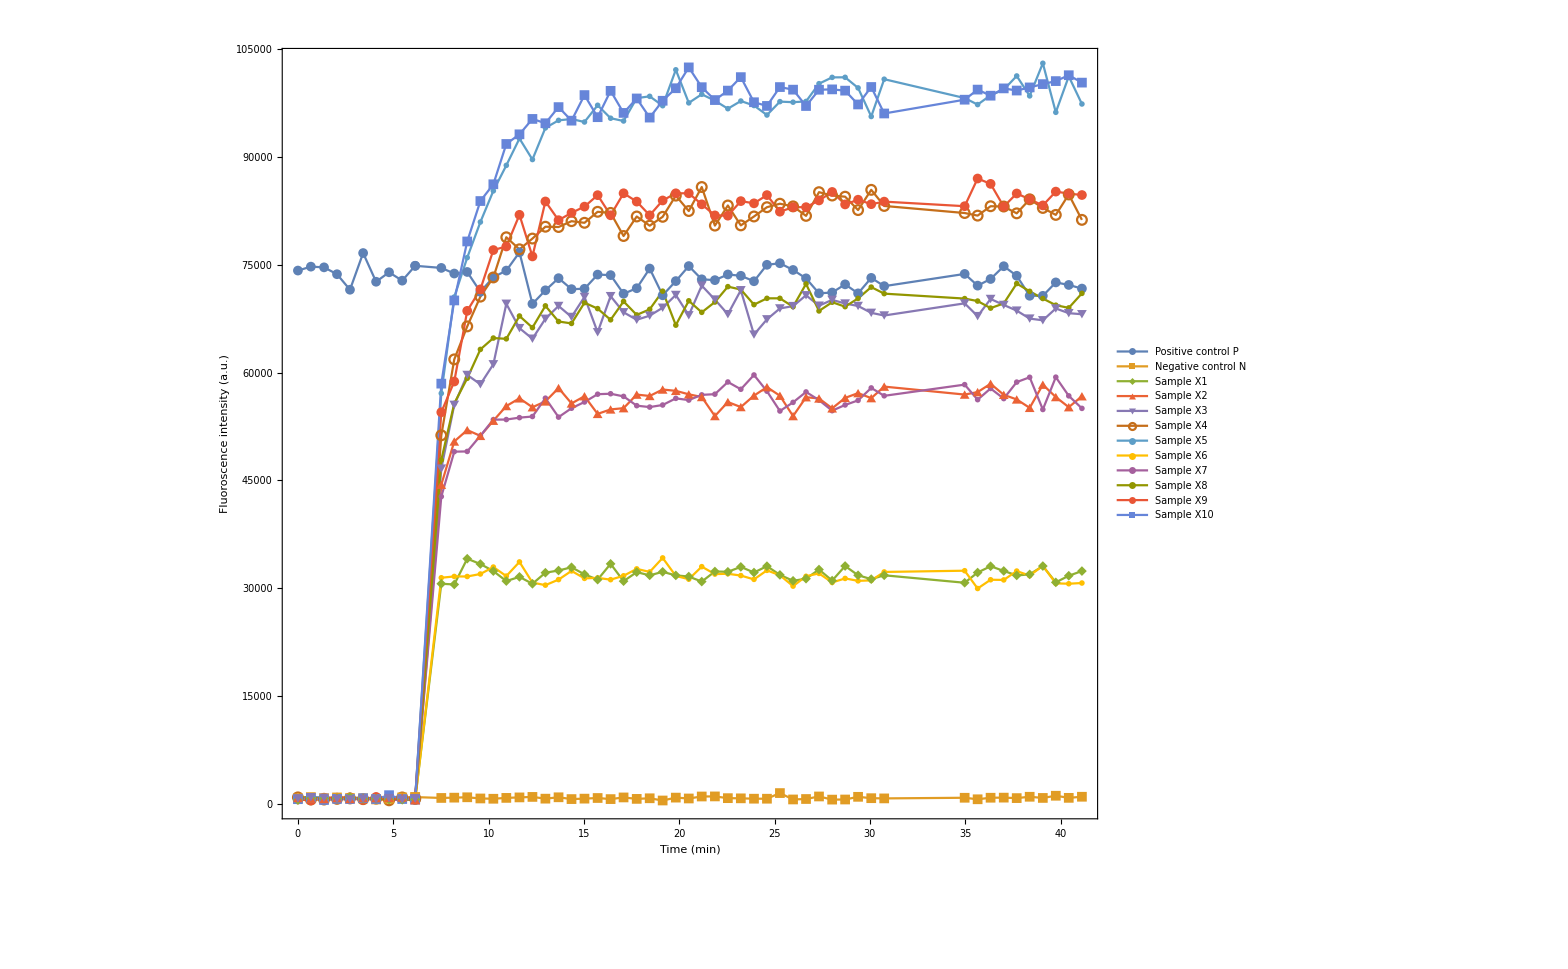

SI\Reporter_Alexa_raw.pdf

```mathematica
siz=10;
fntsz=35;
concV=samplename;
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnew,Joined->True,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[ToString[NumberForm[concV[[1]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[2]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[3]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[4]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[5]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[6]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[7]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[8]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[9]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[10]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[11]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[12]],3]],FontSize->fntsz]
},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,10}]
Export["SI\\Reporter_Alexa_raw.pdf",qs]
```

```mathematica
samplename
```

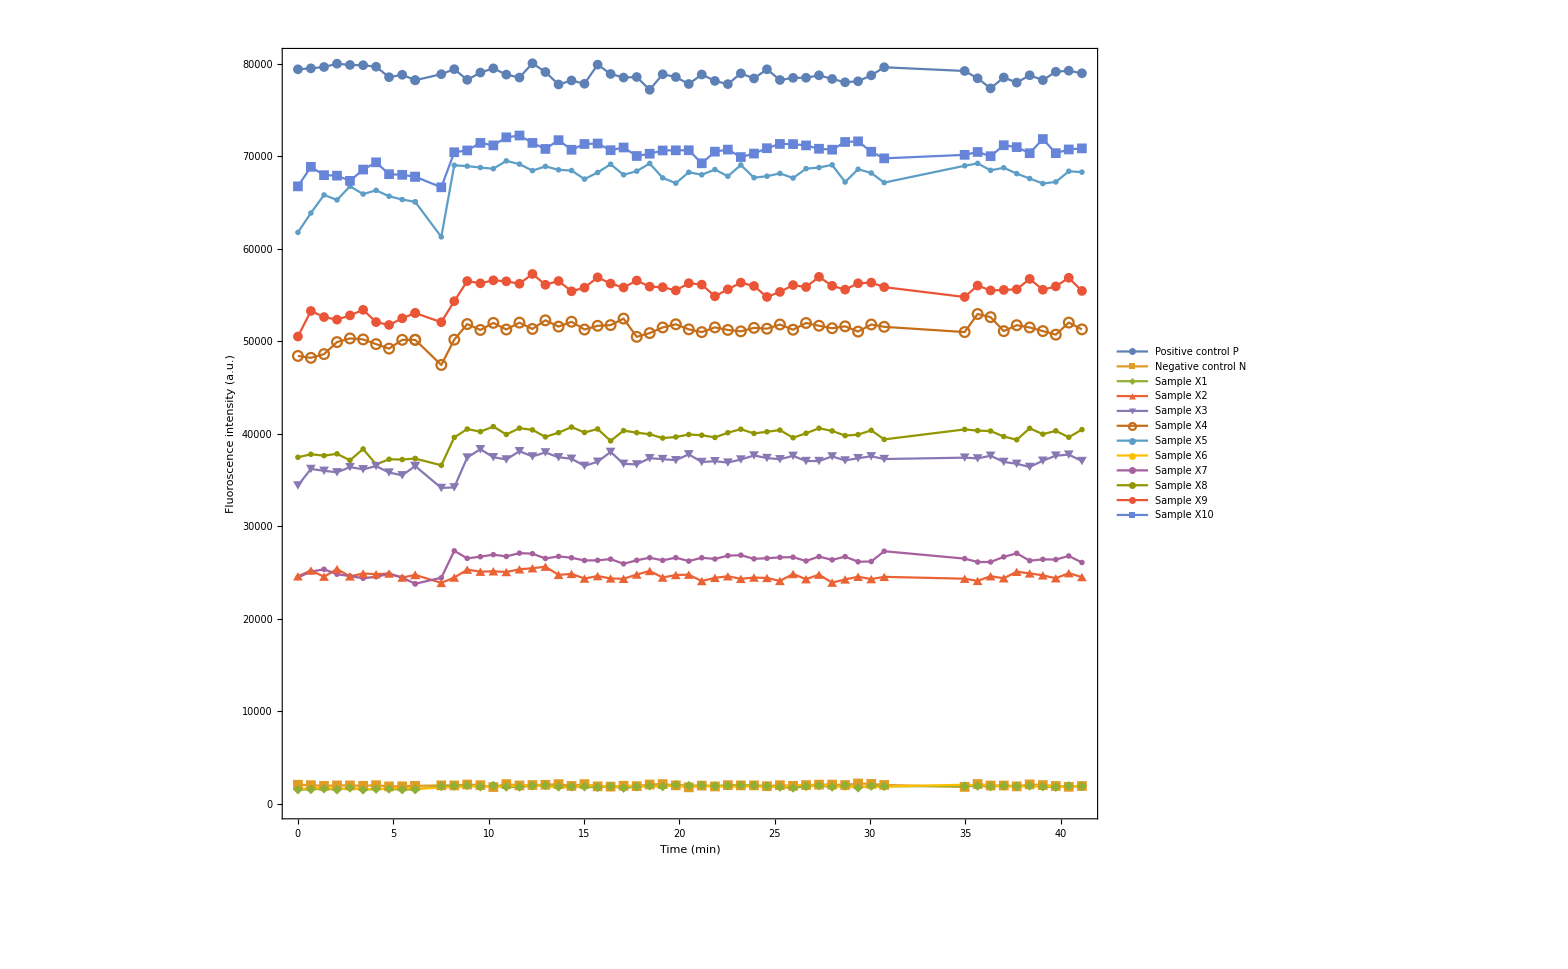

SI\Reporter_Cy3_raw.pdf

```mathematica
siz=10;
fntsz=35;
concV=samplename;
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnewtem,Joined->True,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[ToString[NumberForm[concV[[1]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[2]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[3]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[4]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[5]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[6]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[7]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[8]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[9]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[10]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[11]],3]],FontSize->fntsz],Style[ToString[NumberForm[concV[[12]],3]],FontSize->fntsz]
},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,10}]
Export["SI\\Reporter_Cy3_raw.pdf",qs]
```

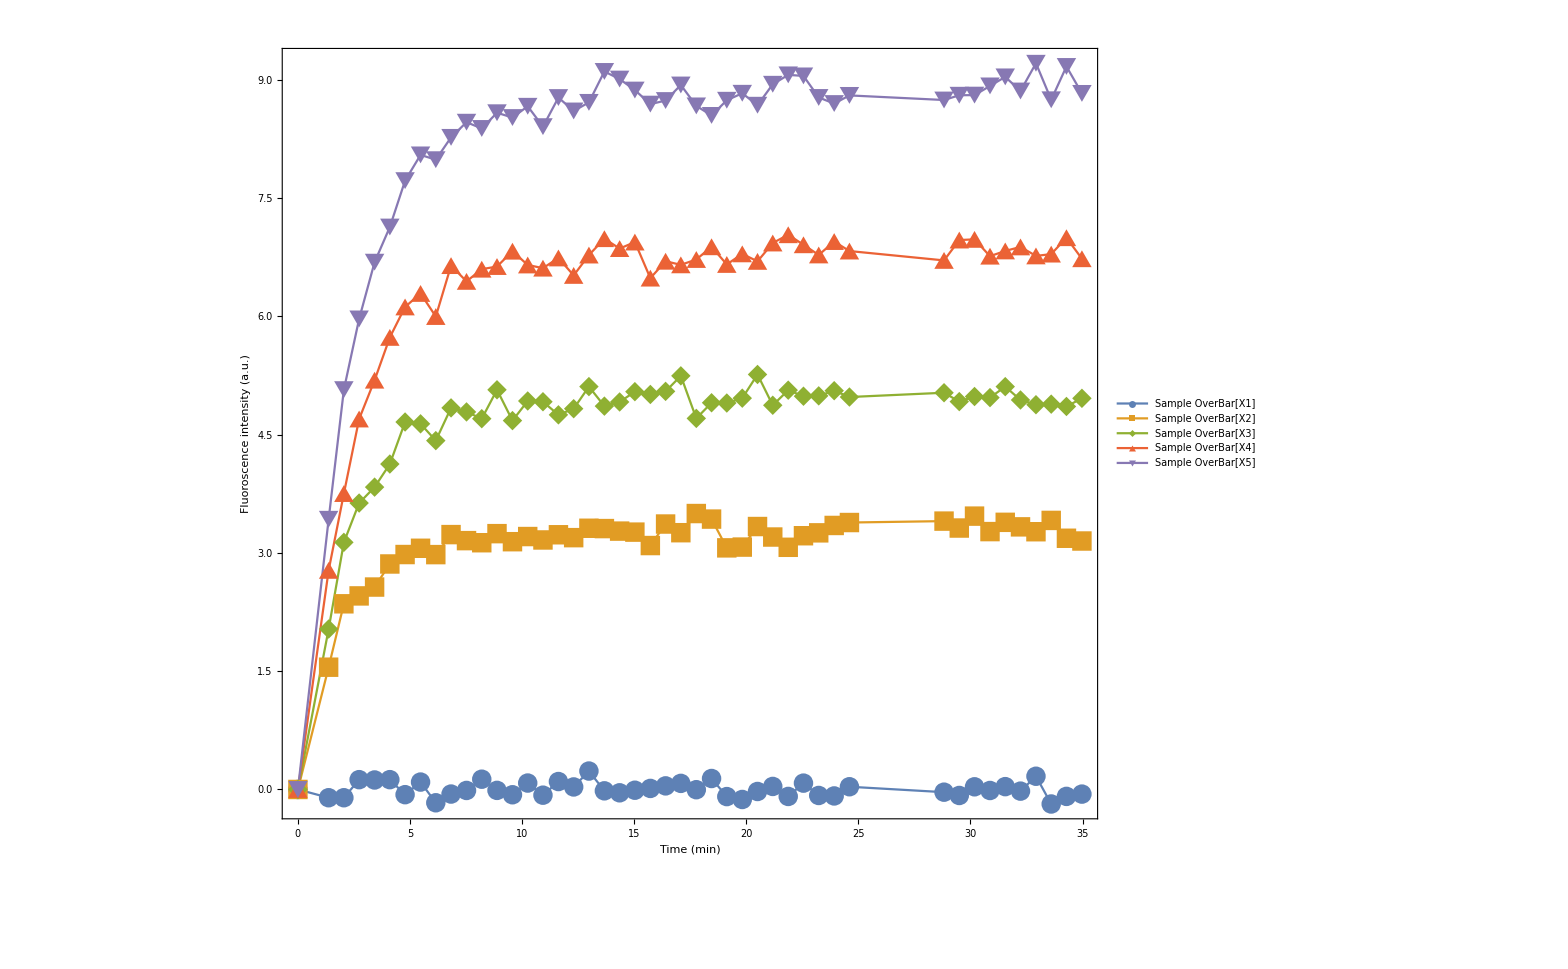

SI\Reporter_Alexa_norm.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnewfl,Joined->True,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 20}]
Export["SI\\Reporter_Alexa_norm.pdf",qs]
```

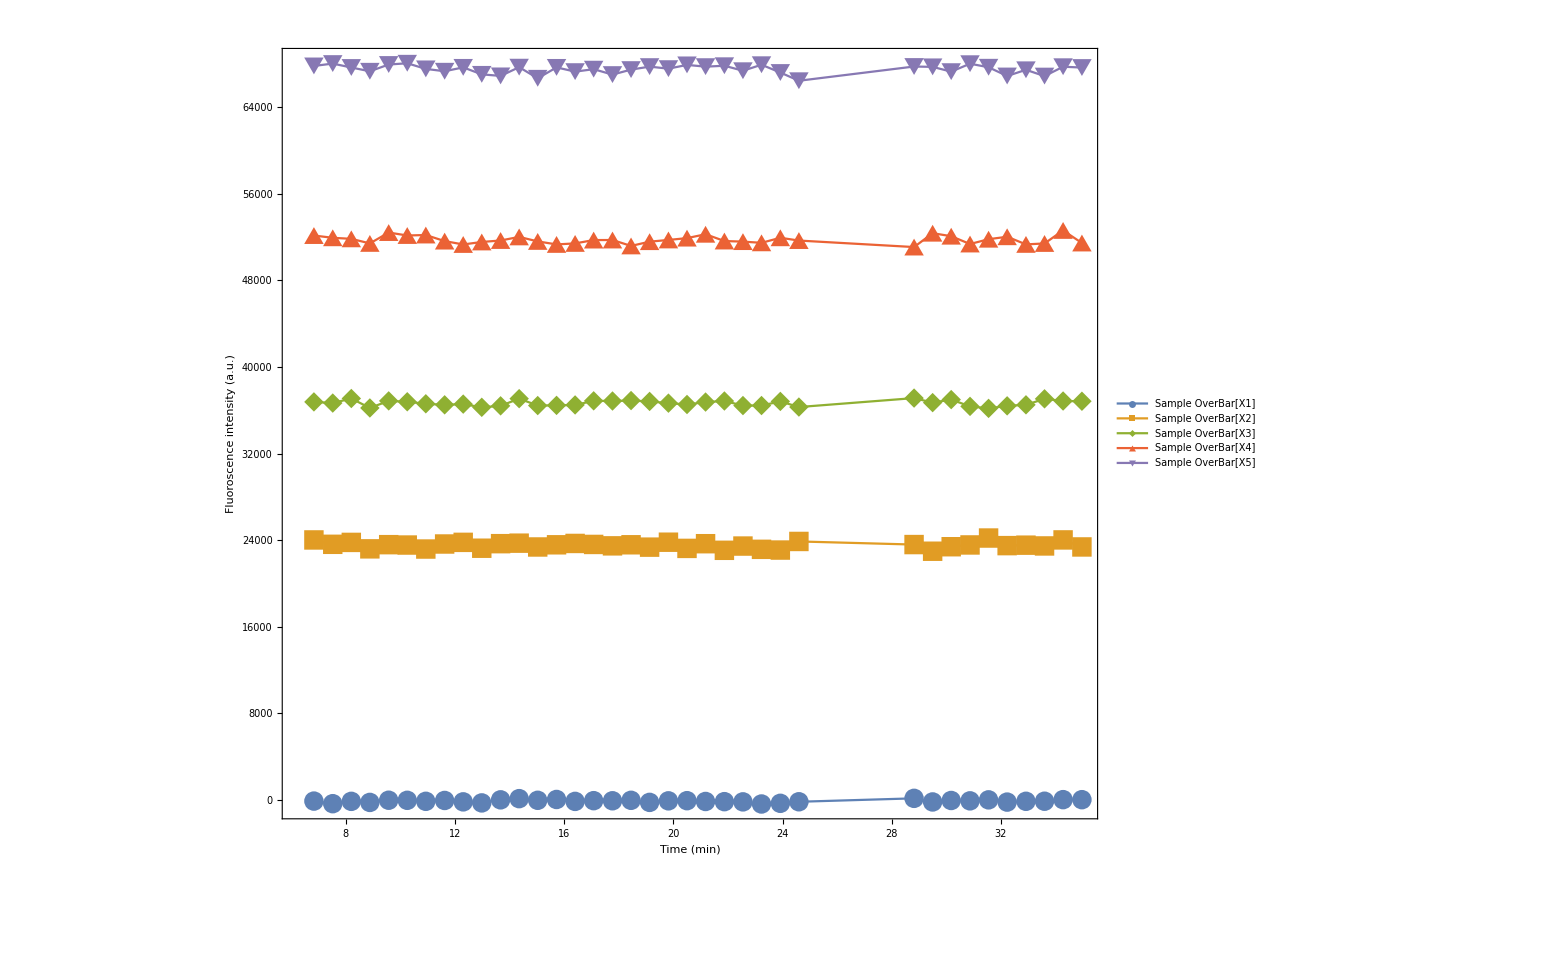

SI\Reporter_Cy3_norm.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnewfltem,Joined->True,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 20}]
Export["SI\\Reporter_Cy3_norm.pdf",qs]
```

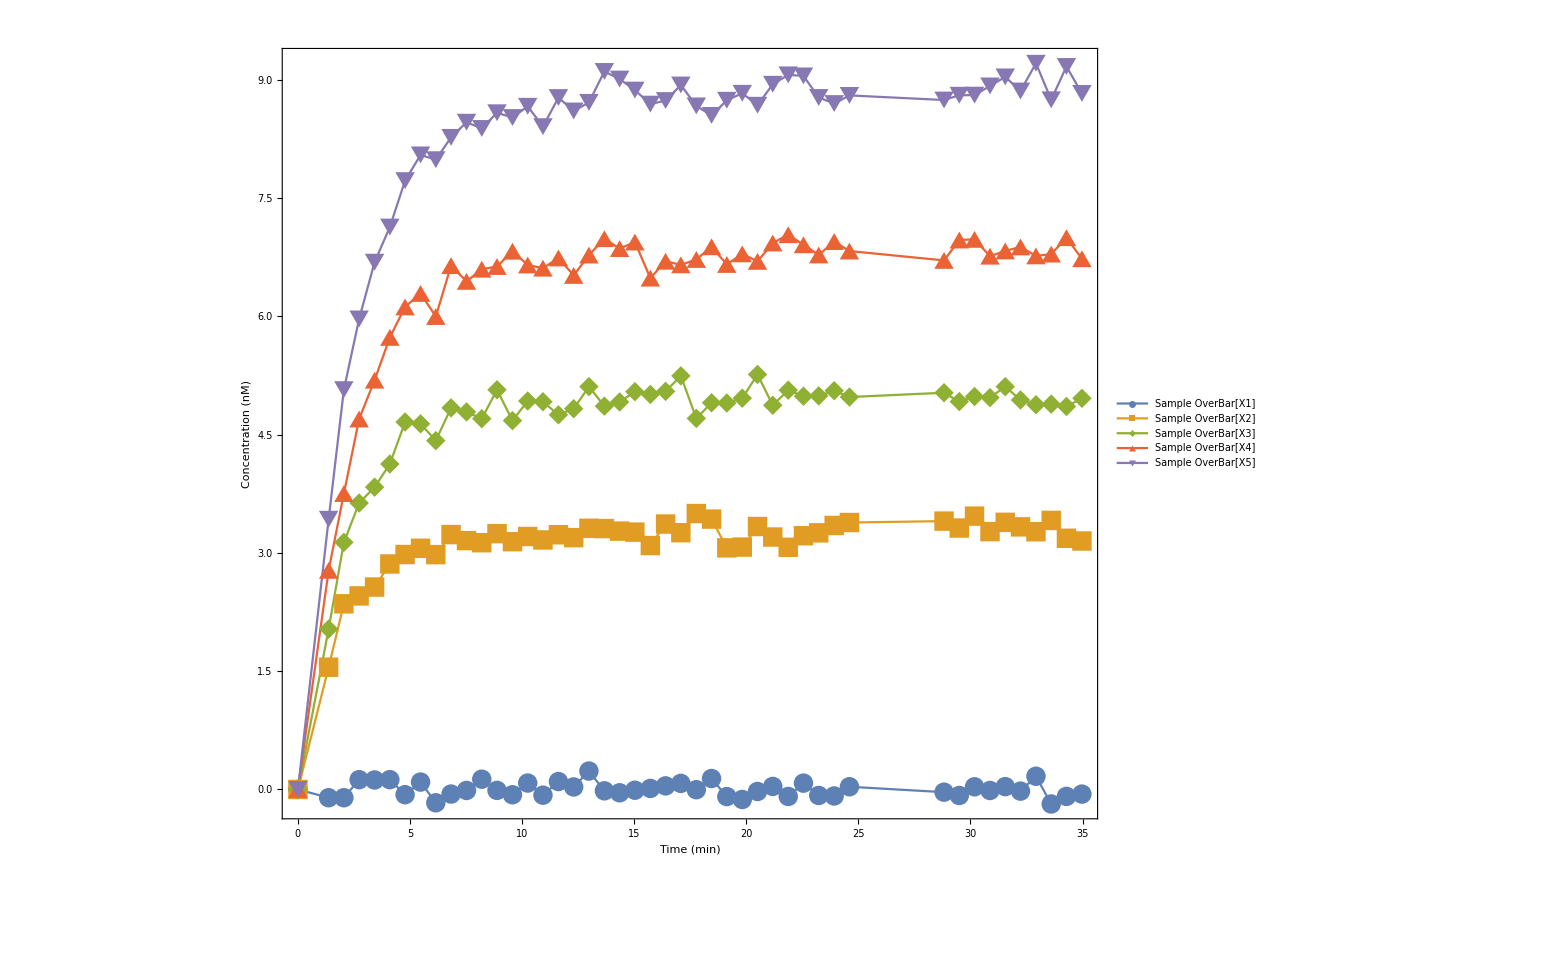

SI\Reporter_Alexa_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnewfl,Joined->True,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 20}]
Export["SI\\Reporter_Alexa_conc.pdf",qs]
```

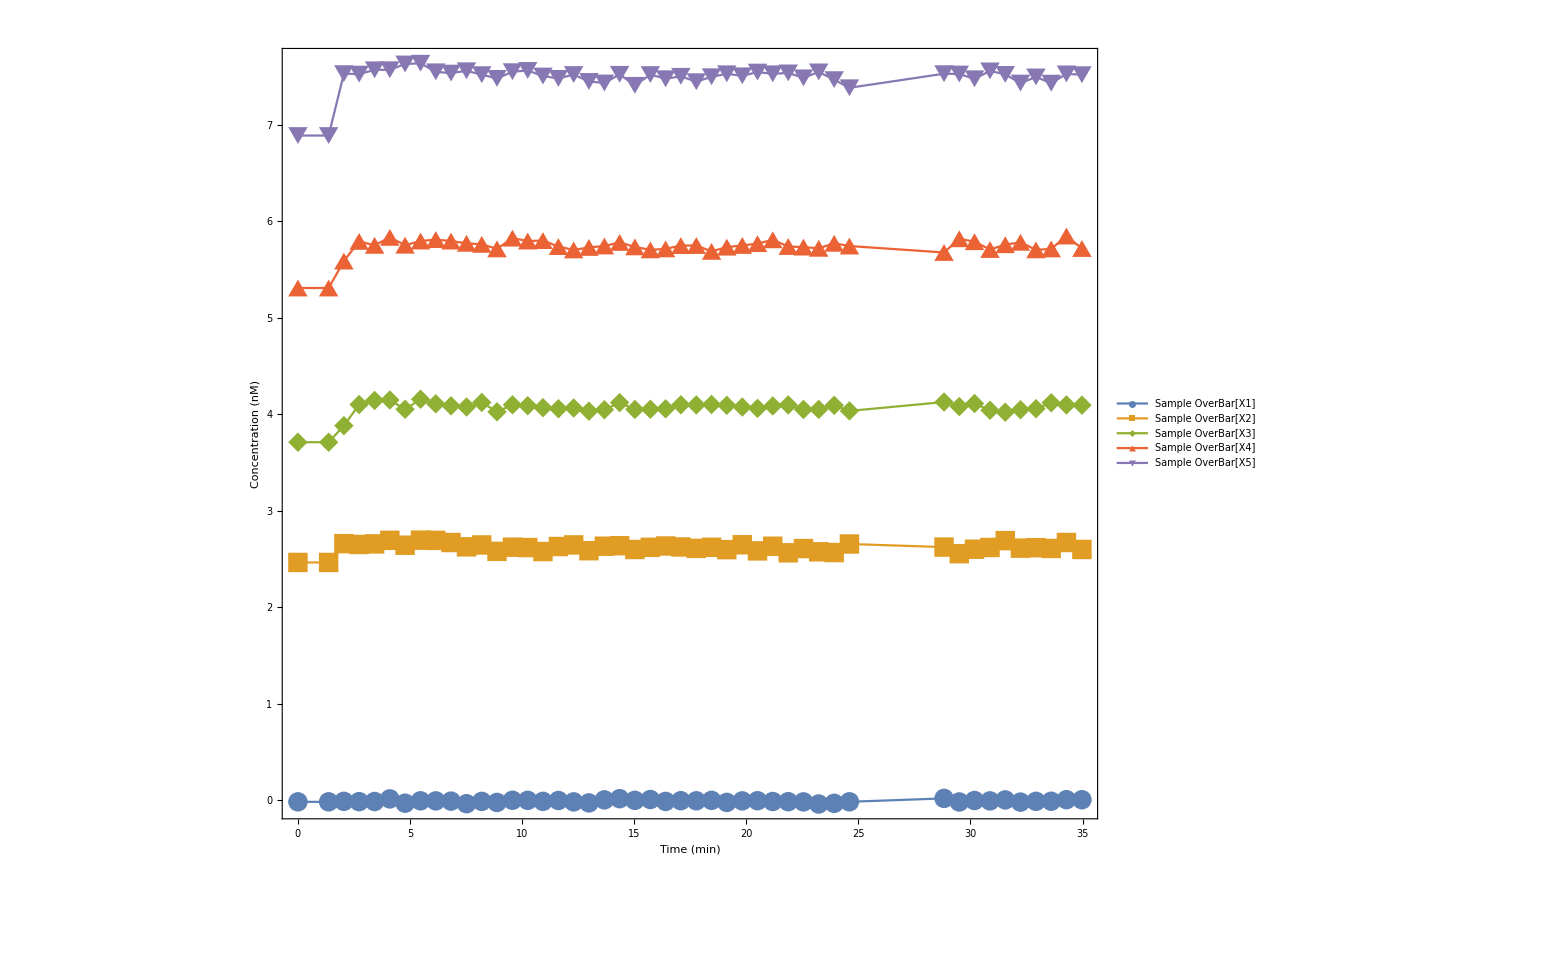

SI\Reporter_Cy3_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dtemp,Joined->True,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 20}]
Export["SI\\Reporter_Cy3_conc.pdf",qs]
```